### 1D Elliptic Theta Lattice: V matrix

NOTE: VV’s that are bad: L=3.5, 4, 4.5, both VV1 and VV2a. Others may be suspect since I don’t understand why AccuracyGoal had such a bad effect in the first place.

```mathematica
Quit[]
```

```mathematica
1/(2*√(2π)*0.4)30
```

14.9603

```mathematica
$HistoryLength=0;
```

#### Define potential

```mathematica
Clear[ϵ,a,LL,V0]
prec=MachinePrecision;

Vx[x_]:=EllipticTheta[3,(π (x(*-1/(√17)a*)))/(2 a),ⅇ^(-(π^2 ϵ^2)/(2 a^2))]
Vz[z_]:=Exp[(-(z(*+1/(√13)a*))^2)/(2 σ^2)](* SWITCHED L/3->a SO POTENTIAL DOESNT DEPEND ON L *)
(* NOTE: -U0 is put in "ET 2D Lattice - S and Heff", to make it easier to change U0 without redoing VV1
	Also note V[x,y,z] isn't really used, because it's cut up in Vmat *)
V1[x_,z_]:=Evaluate@(Vx[x]Vz[z]-V0)

V[{x_,z_}]:=V[x,z]

(* set main parameters *)
ϵ=SetPrecision[0.4,prec];
σ=SetPrecision[0.4,prec];
a=SetPrecision[1.0,prec];
LL=SetPrecision[3.0,prec];

V0=0; (* if this changes, need V0 term in code below *)

(* check Vmax is same as desired (see above) and Vmin is zero *)
Print["V_max=",Vmax=Chop@Maximize[V[x,z],{x,z}][[1]]]
Print["V_min=",Vmin=Chop@Minimize[V[x,z],{x,z}][[1]](*," (=",Vmin,"?)"*)]
Print["Using V0=",V0]
(*Vmax=0; (* hack *)*)

(* get saddle potentials, depends on getting correct saddlepts first *)
saddlePts={{a,0}};
Print["V_(saddle - 1)=",Vsaddle1=V[saddlePts[[1]]]]
```

V_max=V[x,z]

V_min=V[x,z]

Using V0=0

V_(saddle - 1)=V[1.,0]

```mathematica
V1[0,0]*14.960335515053726
```

29.8418

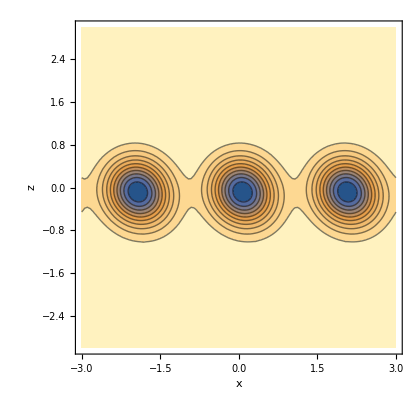

```mathematica
cp=ContourPlot[-14.9603*(V1[x,z]+0.5 V2[x,z]),{x,-3a,3a},{z,-LL,LL},PlotRange->All,LabelStyle->36,Contours->10,FrameLabel->{"x",Rotate["z",-90 Degree]},AspectRatio->1]
```

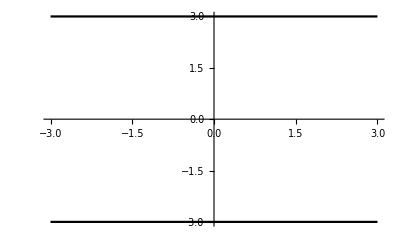

```mathematica
linep=Plot[{LL,-LL},{x,-3,3},PlotStyle->Black]
```

```mathematica
Show[cp,linep,ImageSize->400]
```

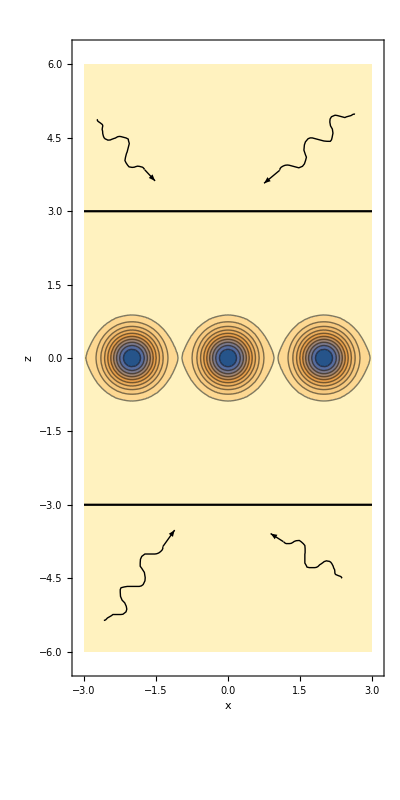

```mathematica
Plot3D[-14.9603*(V1[x,z]+0.5 V2[x,z]),{x,-3a,3a},{z,-LL,LL},PlotRange->All,ColorFunction->(ColorData[{"TemperatureMap",{0,1.2}}][#3]&),PlotStyle->Opacity[0.8],LabelStyle->36,AxesLabel->{"x","z"}]
```

-Graphics3D-

#### Create H matrix, dimension (2Nt+1) x (Nt+1) on each side

Using H_QM=-d^2/dx^2+-d^2/dz^2+V(x,z) and following derivation in Hsu (2005) gives a matrix equation for amplitudes A_n_x(ν,k):

```mathematica
VmatS1=VmatS;
```

```mathematica
Clear[Vxmat,Vymat,Vxymat,Vzmat,VmatS,kx,ky]
Nt=36;

ξ[nz_,z_]:=If[nz==0,1/(√(2LL)),1/(√LL)Cos[(nz π (z+LL))/(2LL)]]
Vxmat=Table[
If[Abs[Δnx]≤6,
NIntegrate[Vx[x] 1/(2a)Exp[I (Δnx)π x/a],{x,-a,a}]
(* else *),0],
{Δnx,-2Nt,2Nt}]; //AbsoluteTiming(* for either x or y *)
Vxmat

(* Vzmat is built as a half-matrix to get 2x efficiency *)
Vzmat=Table[
If[(*EvenQ@Abs[nz-nzp]*)True,(* for ASYM can't skip any -- CAREFUL *)
NIntegrate[Vz[z]ξ[nz,z]ξ[nzp,z],{z,-LL,LL}(*,AccuracyGoal->16*)]
(* else *),0],
{nz,0,Nt},{nzp,0,Nt}];//AbsoluteTiming

(* using V0=0 to skip doing the V0 term -- if V0≠0 I'll need to add that term *)
VmatS=SparseArray@Flatten[ParallelTable[Flatten@Table[
(* note no U0 here, it's in "S and Heff" *)
Vxmat[[nx-nxp+2Nt+1]]Vzmat[[nz+1,nzp+1]]
,{nx,-Nt,Nt},{nz,0,Nt}],{nxp,-Nt,Nt},{nzp,0,Nt}],1];//Timing//AbsoluteTiming
(*Vmat//MatrixForm*)

Vzmat//MatrixForm
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {1.79352×10^-8}. NIntegrate obtained -6.34909×10^-14+4.47781×10^-13 ⅈ and 1.61768×10^-13 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {1.79352×10^-8}. NIntegrate obtained -6.34909×10^-14-4.47781×10^-13 ⅈ and 1.61768×10^-13 for the integral and error estimates.

{0.267057,Null}

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-6.34909×10^-14+4.47781×10^-13 ⅈ,-2.10002×10^-9+1.65743×10^-9 ⅈ,-3.24791×10^-6-3.05551×10^-7 ⅈ,-0.000537685-0.000619207 ⅈ,0.00199248-0.0424523 ⅈ,0.328495-0.313439 ⅈ,1.,0.328495+0.313439 ⅈ,0.00199248+0.0424523 ⅈ,-0.000537685+0.000619207 ⅈ,-3.24791×10^-6+3.05551×10^-7 ⅈ,-2.10002×10^-9-1.65743×10^-9 ⅈ,-6.34909×10^-14-4.47781×10^-13 ⅈ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

{24.6377,Null}

{15.3327,{5.14738,Null}}

(0.100265 | 0.0122423 | -0.135307 | -0.0341308 | 0.117455 | 0.0491203 | -0.0924595 | -0.0551631 | 0.065592 | 0.0528288 | -0.0414497 | -0.0446338 | 0.0228067 | 0.0338124 | -0.0103719 | -0.0231652 | 0.00330187 | 0.0144187 | -0.0000265578 | -0.00816991 | -0.00103049 | 0.00421428 | 0.0010532 | -0.00197513 | -0.000746563 | 0.000837317 | 0.000436394 | -0.000318376 | -0.000221904 | 0.000106864 | 0.000100469 | -0.0000306304 | -0.0000409843 | 6.87935×10^-6 | 0.0000151593 | -8.20551×10^-7 | -5.10045×10^-6
0.0122423 | 0.00458853 | -0.0154774 | -0.0126235 | 0.0105992 | 0.0176743 | -0.00427294 | -0.0189982 | -0.00165059 | 0.0170712 | 0.00579474 | -0.0131826 | -0.00765188 | 0.00879268 | 0.00752871 | -0.0049993 | -0.00618475 | 0.00231599 | 0.00441855 | -0.000747445 | -0.00279705 | 0.0000160615 | 0.00158332 | 0.000216827 | -0.000804555 | -0.000219322 | 0.000366946 | 0.000151667 | -0.000149562 | -0.0000858676 | 0.0000539051 | 0.0000420623 | -0.0000167945 | -0.0000182611 | 4.28422×10^-6 | 7.11265×10^-6 | -7.46812×10^-7
-0.135307 | -0.0154774 | 0.183318 | 0.0433899 | -0.161055 | -0.0631403 | 0.129434 | 0.0720889 | -0.0946881 | -0.0705671 | 0.0625073 | 0.0612646 | -0.0366435 | -0.0479412 | 0.0184615 | 0.0341045 | -0.00735285 | -0.0221573 | 0.00160611 | 0.0131755 | 0.000725948 | -0.00717362 | -0.00125657 | 0.00357202 | 0.0010533 | -0.00162175 | -0.00068481 | 0.000667637 | 0.00037962 | -0.000246785 | -0.00018589 | 0.0000804285 | 0.0000817618 | -0.0000222392 | -0.0000325868 | 4.69784×10^-6 | 0.0000118241
-0.0341308 | -0.0126235 | 0.0433899 | 0.0348864 | -0.0303496 | -0.0492961 | 0.0132215 | 0.0537437 | 0.00317239 | -0.049252 | -0.0150972 | 0.0390465 | 0.0209753 | -0.0269746 | -0.0213653 | 0.016108 | 0.018132 | -0.00806274 | -0.0134003 | 0.0030795 | 0.00879891 | -0.000546679 | -0.00518492 | -0.000420088 | 0.00275482 | 0.000587817 | -0.00132106 | -0.000456857 | 0.000570414 | 0.000279597 | -0.000220262 | -0.000146191 | 0.0000749839 | 0.000067436 | -0.0000218256 | -0.0000278753 | 5.01931×10^-6
0.117455 | 0.0105992 | -0.161055 | -0.0303496 | 0.146646 | 0.0460123 | -0.124986 | -0.055695 | 0.0991798 | 0.0586423 | -0.0727128 | -0.0553865 | 0.0487153 | 0.0475512 | -0.0293282 | -0.0373379 | 0.0153981 | 0.0268889 | -0.00658935 | -0.0177769 | 0.00180687 | 0.0107876 | 0.000289798 | -0.00600212 | -0.000885576 | 0.00305551 | 0.00081577 | -0.00141829 | -0.00055688 | 0.000596937 | 0.000319296 | -0.000225706 | -0.000160517 | 0.0000753975 | 0.0000721475 | -0.0000215041 | -0.0000292882
0.0491203 | 0.0176743 | -0.0631403 | -0.0492961 | 0.0460123 | 0.0709557 | -0.0229042 | -0.0795498 | -0.000225089 | 0.075719 | 0.018353 | -0.063044 | -0.0288107 | 0.0463618 | 0.0315786 | -0.0300381 | -0.0285809 | 0.0168715 | 0.0225124 | -0.00786198 | -0.0157882 | 0.00264335 | 0.00997041 | -0.000175689 | -0.00570143 | -0.000657623 | 0.00295829 | 0.000715747 | -0.00139176 | -0.00051718 | 0.000591492 | 0.000304971 | -0.000225293 | -0.000155805 | 0.000075719 | 0.0000707346 | -0.000021731
-0.0924595 | -0.00427294 | 0.129434 | 0.0132215 | -0.124986 | -0.0229042 | 0.116392 | 0.0325656 | -0.103011 | -0.0405144 | 0.0853879 | 0.0449288 | -0.0653975 | -0.0447832 | 0.0456519 | 0.0403356 | -0.0285647 | -0.0329575 | 0.0155989 | 0.0245011 | -0.0070255 | -0.0166054 | 0.00217786 | 0.0102711 | 0.0000522633 | -0.00579865 | -0.000757646 | 0.00298481 | 0.000755446 | -0.00139721 | -0.000531506 | 0.000591906 | 0.000309682 | -0.000224971 | -0.000157218 | 0.000075492 | 0.0000711204
-0.0551631 | -0.0189982 | 0.0720889 | 0.0537437 | -0.055695 | -0.0795498 | 0.0325656 | 0.0929311 | -0.00772365 | -0.0933418 | -0.0139385 | 0.0830343 | 0.0289563 | -0.0661074 | -0.0360263 | 0.0471253 | 0.035959 | -0.0298373 | -0.0309688 | 0.0164353 | 0.0236839 | -0.00749099 | -0.0163047 | 0.00240582 | 0.0101739 | -0.0000477595 | -0.00577213 | -0.000717947 | 0.00297937 | 0.000741121 | -0.00139679 | -0.000526795 | 0.000592227 | 0.000308269 | -0.000225198 | -0.000156832 | 0.0000755901
0.065592 | -0.00165059 | -0.0946881 | 0.00317239 | 0.0991798 | -0.000225089 | -0.103011 | -0.00772365 | 0.1026 | 0.0188522 | -0.0956954 | -0.0299111 | 0.0823244 | 0.0377132 | -0.064634 | -0.0404028 | 0.0458526 | 0.0379477 | -0.0290008 | -0.031786 | 0.0159698 | 0.0239846 | -0.00726303 | -0.0164019 | 0.00230579 | 0.0102004 | -8.06001×10^-6 | -0.00577758 | -0.000732272 | 0.00297978 | 0.000745832 | -0.00139647 | -0.000528208 | 0.000592 | 0.000308655 | -0.0002251 | -0.000156928
0.0528288 | 0.0170712 | -0.0705671 | -0.049252 | 0.0586423 | 0.075719 | -0.0405144 | -0.0933418 | 0.0188522 | 0.100246 | 0.00287965 | -0.0964053 | -0.0211541 | 0.0837978 | 0.0333366 | -0.0659067 | -0.0384141 | 0.0466891 | 0.0371305 | -0.0294663 | -0.0314853 | 0.0161978 | 0.0238873 | -0.00736306 | -0.0163754 | 0.00234549 | 0.010195 | -0.0000223858 | -0.00577716 | -0.000727561 | 0.0029801 | 0.000744419 | -0.0013967 | -0.000527822 | 0.000592099 | 0.00030856 | -0.000225134
-0.0414497 | 0.00579474 | 0.0625073 | -0.0150972 | -0.0727128 | 0.018353 | 0.0853879 | -0.0139385 | -0.0956954 | 0.00287965 | 0.0995365 | 0.0116366 | -0.0949319 | -0.0255307 | 0.0825252 | 0.0353253 | -0.0650702 | -0.0392313 | 0.0462236 | 0.0374312 | -0.0292383 | -0.0315825 | 0.0160978 | 0.0239139 | -0.00732336 | -0.0163809 | 0.00233117 | 0.0101954 | -0.0000176743 | -0.00577684 | -0.000728974 | 0.00297987 | 0.000744805 | -0.0013966 | -0.000527917 | 0.000592064 | 0.000308581
-0.0446338 | -0.0131826 | 0.0612646 | 0.0390465 | -0.0553865 | -0.063044 | 0.0449288 | 0.0830343 | -0.0299111 | -0.0964053 | 0.0116366 | 0.10101 | 0.00726001 | -0.0962045 | -0.023542 | 0.0833617 | 0.0345081 | -0.0655357 | -0.0389306 | 0.0464516 | 0.037334 | -0.0293384 | -0.031556 | 0.0161375 | 0.0239084 | -0.00733768 | -0.0163805 | 0.00233588 | 0.0101957 | -0.0000190872 | -0.00577707 | -0.000728588 | 0.00297997 | 0.000744709 | -0.00139664 | -0.000527896 | 0.000592075
0.0228067 | -0.00765188 | -0.0366435 | 0.0209753 | 0.0487153 | -0.0288107 | -0.0653975 | 0.0289563 | 0.0823244 | -0.0211541 | -0.0949319 | 0.00726001 | 0.0997372 | 0.00924871 | -0.095368 | -0.0243592 | 0.0828962 | 0.0348088 | -0.0653077 | -0.0390279 | 0.0463516 | 0.0373605 | -0.0292987 | -0.0315615 | 0.0161232 | 0.0239088 | -0.00733297 | -0.0163801 | 0.00233447 | 0.0101955 | -0.0000187014 | -0.00577697 | -0.000728683 | 0.00297994 | 0.000744731 | -0.00139663 | -0.0005279
0.0338124 | 0.00879268 | -0.0479412 | -0.0269746 | 0.0475512 | 0.0463618 | -0.0447832 | -0.0661074 | 0.0377132 | 0.0837978 | -0.0255307 | -0.0962045 | 0.00924871 | 0.100574 | 0.00843151 | -0.0958335 | -0.0240585 | 0.0831241 | 0.0347116 | -0.0654077 | -0.0390013 | 0.0463913 | 0.037355 | -0.029313 | -0.031561 | 0.0161279 | 0.0239092 | -0.00733438 | -0.0163804 | 0.00233485 | 0.0101956 | -0.000018797 | -0.005777 | -0.000728662 | 0.00297995 | 0.000744727 | -0.00139663
-0.0103719 | 0.00752871 | 0.0184615 | -0.0213653 | -0.0293282 | 0.0315786 | 0.0456519 | -0.0360263 | -0.064634 | 0.0333366 | 0.0825252 | -0.023542 | -0.095368 | 0.00843151 | 0.100108 | 0.00873221 | -0.0956056 | -0.0241557 | 0.0830241 | 0.0347381 | -0.065368 | -0.0390068 | 0.0463769 | 0.0373555 | -0.0293083 | -0.0315607 | 0.0161264 | 0.0239089 | -0.007334 | -0.0163803 | 0.00233476 | 0.0101955 | -0.0000187756 | -0.00577699 | -0.000728666 | 0.00297995 | 0.000744727
-0.0231652 | -0.0049993 | 0.0341045 | 0.016108 | -0.0373379 | -0.0300381 | 0.0403356 | 0.0471253 | -0.0404028 | -0.0659067 | 0.0353253 | 0.0833617 | -0.0243592 | -0.0958335 | 0.00873221 | 0.100336 | 0.00863498 | -0.0957056 | -0.0241292 | 0.0830638 | 0.0347327 | -0.0653824 | -0.0390064 | 0.0463817 | 0.0373558 | -0.0293097 | -0.0315609 | 0.0161268 | 0.023909 | -0.00733409 | -0.0163803 | 0.00233478 | 0.0101955 | -0.0000187799 | -0.005777 | -0.000728666 | 0.00297995
0.00330187 | -0.00618475 | -0.00735285 | 0.018132 | 0.0153981 | -0.0285809 | -0.0285647 | 0.035959 | 0.0458526 | -0.0384141 | -0.0650702 | 0.0345081 | 0.0828962 | -0.0240585 | -0.0956056 | 0.00863498 | 0.100236 | 0.00866151 | -0.0956659 | -0.0241347 | 0.0830495 | 0.0347331 | -0.0653776 | -0.0390061 | 0.0463802 | 0.0373555 | -0.0293093 | -0.0315608 | 0.0161267 | 0.023909 | -0.00733407 | -0.0163803 | 0.00233477 | 0.0101955 | -0.0000187791 | -0.005777 | -0.000728666
0.0144187 | 0.00231599 | -0.0221573 | -0.00806274 | 0.0268889 | 0.0168715 | -0.0329575 | -0.0298373 | 0.0379477 | 0.0466891 | -0.0392313 | -0.0655357 | 0.0348088 | 0.0831241 | -0.0241557 | -0.0957056 | 0.00866151 | 0.100276 | 0.00865606 | -0.0956802 | -0.0241343 | 0.0830542 | 0.0347334 | -0.0653791 | -0.0390063 | 0.0463806 | 0.0373556 | -0.0293094 | -0.0315609 | 0.0161268 | 0.023909 | -0.00733408 | -0.0163803 | 0.00233477 | 0.0101955 | -0.0000187792 | -0.005777
-0.0000265578 | 0.00441855 | 0.00160611 | -0.0134003 | -0.00658935 | 0.0225124 | 0.0155989 | -0.0309688 | -0.0290008 | 0.0371305 | 0.0462236 | -0.0389306 | -0.0653077 | 0.0347116 | 0.0830241 | -0.0241292 | -0.0956659 | 0.00865606 | 0.100262 | 0.00865647 | -0.0956755 | -0.0241339 | 0.0830528 | 0.0347332 | -0.0653787 | -0.0390062 | 0.0463805 | 0.0373556 | -0.0293094 | -0.0315609 | 0.0161268 | 0.023909 | -0.00733408 | -0.0163803 | 0.00233477 | 0.0101955 | -0.0000187792
-0.00816991 | -0.000747445 | 0.0131755 | 0.0030795 | -0.0177769 | -0.00786198 | 0.0245011 | 0.0164353 | -0.031786 | -0.0294663 | 0.0374312 | 0.0464516 | -0.0390279 | -0.0654077 | 0.0347381 | 0.0830638 | -0.0241347 | -0.0956802 | 0.00865647 | 0.100266 | 0.0086568 | -0.0956769 | -0.0241342 | 0.0830532 | 0.0347333 | -0.0653788 | -0.0390062 | 0.0463805 | 0.0373556 | -0.0293094 | -0.0315609 | 0.0161268 | 0.023909 | -0.00733408 | -0.0163803 | 0.00233477 | 0.0101955
-0.00103049 | -0.00279705 | 0.000725948 | 0.00879891 | 0.00180687 | -0.0157882 | -0.0070255 | 0.0236839 | 0.0159698 | -0.0314853 | -0.0292383 | 0.037334 | 0.0463516 | -0.0390013 | -0.065368 | 0.0347327 | 0.0830495 | -0.0241343 | -0.0956755 | 0.0086568 | 0.100265 | 0.00865657 | -0.0956765 | -0.0241341 | 0.0830531 | 0.0347333 | -0.0653788 | -0.0390062 | 0.0463805 | 0.0373556 | -0.0293094 | -0.0315609 | 0.0161268 | 0.023909 | -0.00733408 | -0.0163803 | 0.00233477
0.00421428 | 0.0000160615 | -0.00717362 | -0.000546679 | 0.0107876 | 0.00264335 | -0.0166054 | -0.00749099 | 0.0239846 | 0.0161978 | -0.0315825 | -0.0293384 | 0.0373605 | 0.0463913 | -0.0390068 | -0.0653824 | 0.0347331 | 0.0830542 | -0.0241339 | -0.0956769 | 0.00865657 | 0.100265 | 0.00865667 | -0.0956766 | -0.0241341 | 0.0830531 | 0.0347333 | -0.0653788 | -0.0390062 | 0.0463805 | 0.0373556 | -0.0293094 | -0.0315609 | 0.0161268 | 0.023909 | -0.00733408 | -0.0163803
0.0010532 | 0.00158332 | -0.00125657 | -0.00518492 | 0.000289798 | 0.00997041 | 0.00217786 | -0.0163047 | -0.00726303 | 0.0238873 | 0.0160978 | -0.031556 | -0.0292987 | 0.037355 | 0.0463769 | -0.0390064 | -0.0653776 | 0.0347334 | 0.0830528 | -0.0241342 | -0.0956765 | 0.00865667 | 0.100265 | 0.00865663 | -0.0956766 | -0.0241341 | 0.0830531 | 0.0347333 | -0.0653788 | -0.0390062 | 0.0463805 | 0.0373556 | -0.0293094 | -0.0315609 | 0.0161268 | 0.023909 | -0.00733408
-0.00197513 | 0.000216827 | 0.00357202 | -0.000420088 | -0.00600212 | -0.000175689 | 0.0102711 | 0.00240582 | -0.0164019 | -0.00736306 | 0.0239139 | 0.0161375 | -0.0315615 | -0.029313 | 0.0373555 | 0.0463817 | -0.0390061 | -0.0653791 | 0.0347332 | 0.0830532 | -0.0241341 | -0.0956766 | 0.00865663 | 0.100265 | 0.00865664 | -0.0956766 | -0.0241341 | 0.0830531 | 0.0347333 | -0.0653788 | -0.0390062 | 0.0463805 | 0.0373556 | -0.0293094 | -0.0315609 | 0.0161268 | 0.023909
-0.000746563 | -0.000804555 | 0.0010533 | 0.00275482 | -0.000885576 | -0.00570143 | 0.0000522633 | 0.0101739 | 0.00230579 | -0.0163754 | -0.00732336 | 0.0239084 | 0.0161232 | -0.031561 | -0.0293083 | 0.0373558 | 0.0463802 | -0.0390063 | -0.0653787 | 0.0347333 | 0.0830531 | -0.0241341 | -0.0956766 | 0.00865664 | 0.100265 | 0.00865664 | -0.0956766 | -0.0241341 | 0.0830531 | 0.0347333 | -0.0653788 | -0.0390062 | 0.0463805 | 0.0373556 | -0.0293094 | -0.0315609 | 0.0161268
0.000837317 | -0.000219322 | -0.00162175 | 0.000587817 | 0.00305551 | -0.000657623 | -0.00579865 | -0.0000477595 | 0.0102004 | 0.00234549 | -0.0163809 | -0.00733768 | 0.0239088 | 0.0161279 | -0.0315607 | -0.0293097 | 0.0373555 | 0.0463806 | -0.0390062 | -0.0653788 | 0.0347333 | 0.0830531 | -0.0241341 | -0.0956766 | 0.00865664 | 0.100265 | 0.00865664 | -0.0956766 | -0.0241341 | 0.0830531 | 0.0347333 | -0.0653788 | -0.0390062 | 0.0463805 | 0.0373556 | -0.0293094 | -0.0315609
0.000436394 | 0.000366946 | -0.00068481 | -0.00132106 | 0.00081577 | 0.00295829 | -0.000757646 | -0.00577213 | -8.06001×10^-6 | 0.010195 | 0.00233117 | -0.0163805 | -0.00733297 | 0.0239092 | 0.0161264 | -0.0315609 | -0.0293093 | 0.0373556 | 0.0463805 | -0.0390062 | -0.0653788 | 0.0347333 | 0.0830531 | -0.0241341 | -0.0956766 | 0.00865664 | 0.100265 | 0.00865664 | -0.0956766 | -0.0241341 | 0.0830531 | 0.0347333 | -0.0653788 | -0.0390062 | 0.0463805 | 0.0373556 | -0.0293094
-0.000318376 | 0.000151667 | 0.000667637 | -0.000456857 | -0.00141829 | 0.000715747 | 0.00298481 | -0.000717947 | -0.00577758 | -0.0000223858 | 0.0101954 | 0.00233588 | -0.0163801 | -0.00733438 | 0.0239089 | 0.0161268 | -0.0315608 | -0.0293094 | 0.0373556 | 0.0463805 | -0.0390062 | -0.0653788 | 0.0347333 | 0.0830531 | -0.0241341 | -0.0956766 | 0.00865664 | 0.100265 | 0.00865664 | -0.0956766 | -0.0241341 | 0.0830531 | 0.0347333 | -0.0653788 | -0.0390062 | 0.0463805 | 0.0373556
-0.000221904 | -0.000149562 | 0.00037962 | 0.000570414 | -0.00055688 | -0.00139176 | 0.000755446 | 0.00297937 | -0.000732272 | -0.00577716 | -0.0000176743 | 0.0101957 | 0.00233447 | -0.0163804 | -0.007334 | 0.023909 | 0.0161267 | -0.0315609 | -0.0293094 | 0.0373556 | 0.0463805 | -0.0390062 | -0.0653788 | 0.0347333 | 0.0830531 | -0.0241341 | -0.0956766 | 0.00865664 | 0.100265 | 0.00865664 | -0.0956766 | -0.0241341 | 0.0830531 | 0.0347333 | -0.0653788 | -0.0390062 | 0.0463805
0.000106864 | -0.0000858676 | -0.000246785 | 0.000279597 | 0.000596937 | -0.00051718 | -0.00139721 | 0.000741121 | 0.00297978 | -0.000727561 | -0.00577684 | -0.0000190872 | 0.0101955 | 0.00233485 | -0.0163803 | -0.00733409 | 0.023909 | 0.0161268 | -0.0315609 | -0.0293094 | 0.0373556 | 0.0463805 | -0.0390062 | -0.0653788 | 0.0347333 | 0.0830531 | -0.0241341 | -0.0956766 | 0.00865664 | 0.100265 | 0.00865664 | -0.0956766 | -0.0241341 | 0.0830531 | 0.0347333 | -0.0653788 | -0.0390062
0.000100469 | 0.0000539051 | -0.00018589 | -0.000220262 | 0.000319296 | 0.000591492 | -0.000531506 | -0.00139679 | 0.000745832 | 0.0029801 | -0.000728974 | -0.00577707 | -0.0000187014 | 0.0101956 | 0.00233476 | -0.0163803 | -0.00733407 | 0.023909 | 0.0161268 | -0.0315609 | -0.0293094 | 0.0373556 | 0.0463805 | -0.0390062 | -0.0653788 | 0.0347333 | 0.0830531 | -0.0241341 | -0.0956766 | 0.00865664 | 0.100265 | 0.00865664 | -0.0956766 | -0.0241341 | 0.0830531 | 0.0347333 | -0.0653788
-0.0000306304 | 0.0000420623 | 0.0000804285 | -0.000146191 | -0.000225706 | 0.000304971 | 0.000591906 | -0.000526795 | -0.00139647 | 0.000744419 | 0.00297987 | -0.000728588 | -0.00577697 | -0.000018797 | 0.0101955 | 0.00233478 | -0.0163803 | -0.00733408 | 0.023909 | 0.0161268 | -0.0315609 | -0.0293094 | 0.0373556 | 0.0463805 | -0.0390062 | -0.0653788 | 0.0347333 | 0.0830531 | -0.0241341 | -0.0956766 | 0.00865664 | 0.100265 | 0.00865664 | -0.0956766 | -0.0241341 | 0.0830531 | 0.0347333
-0.0000409843 | -0.0000167945 | 0.0000817618 | 0.0000749839 | -0.000160517 | -0.000225293 | 0.000309682 | 0.000592227 | -0.000528208 | -0.0013967 | 0.000744805 | 0.00297997 | -0.000728683 | -0.005777 | -0.0000187756 | 0.0101955 | 0.00233477 | -0.0163803 | -0.00733408 | 0.023909 | 0.0161268 | -0.0315609 | -0.0293094 | 0.0373556 | 0.0463805 | -0.0390062 | -0.0653788 | 0.0347333 | 0.0830531 | -0.0241341 | -0.0956766 | 0.00865664 | 0.100265 | 0.00865664 | -0.0956766 | -0.0241341 | 0.0830531
6.87935×10^-6 | -0.0000182611 | -0.0000222392 | 0.000067436 | 0.0000753975 | -0.000155805 | -0.000224971 | 0.000308269 | 0.000592 | -0.000527822 | -0.0013966 | 0.000744709 | 0.00297994 | -0.000728662 | -0.00577699 | -0.0000187799 | 0.0101955 | 0.00233477 | -0.0163803 | -0.00733408 | 0.023909 | 0.0161268 | -0.0315609 | -0.0293094 | 0.0373556 | 0.0463805 | -0.0390062 | -0.0653788 | 0.0347333 | 0.0830531 | -0.0241341 | -0.0956766 | 0.00865664 | 0.100265 | 0.00865664 | -0.0956766 | -0.0241341
0.0000151593 | 4.28422×10^-6 | -0.0000325868 | -0.0000218256 | 0.0000721475 | 0.000075719 | -0.000157218 | -0.000225198 | 0.000308655 | 0.000592099 | -0.000527917 | -0.00139664 | 0.000744731 | 0.00297995 | -0.000728666 | -0.005777 | -0.0000187791 | 0.0101955 | 0.00233477 | -0.0163803 | -0.00733408 | 0.023909 | 0.0161268 | -0.0315609 | -0.0293094 | 0.0373556 | 0.0463805 | -0.0390062 | -0.0653788 | 0.0347333 | 0.0830531 | -0.0241341 | -0.0956766 | 0.00865664 | 0.100265 | 0.00865664 | -0.0956766
-8.20551×10^-7 | 7.11265×10^-6 | 4.69784×10^-6 | -0.0000278753 | -0.0000215041 | 0.0000707346 | 0.000075492 | -0.000156832 | -0.0002251 | 0.00030856 | 0.000592064 | -0.000527896 | -0.00139663 | 0.000744727 | 0.00297995 | -0.000728666 | -0.005777 | -0.0000187792 | 0.0101955 | 0.00233477 | -0.0163803 | -0.00733408 | 0.023909 | 0.0161268 | -0.0315609 | -0.0293094 | 0.0373556 | 0.0463805 | -0.0390062 | -0.0653788 | 0.0347333 | 0.0830531 | -0.0241341 | -0.0956766 | 0.00865664 | 0.100265 | 0.00865664
-5.10045×10^-6 | -7.46812×10^-7 | 0.0000118241 | 5.01931×10^-6 | -0.0000292882 | -0.000021731 | 0.0000711204 | 0.0000755901 | -0.000156928 | -0.000225134 | 0.000308581 | 0.000592075 | -0.0005279 | -0.00139663 | 0.000744727 | 0.00297995 | -0.000728666 | -0.005777 | -0.0000187792 | 0.0101955 | 0.00233477 | -0.0163803 | -0.00733408 | 0.023909 | 0.0161268 | -0.0315609 | -0.0293094 | 0.0373556 | 0.0463805 | -0.0390062 | -0.0653788 | 0.0347333 | 0.0830531 | -0.0241341 | -0.0956766 | 0.00865664 | 0.100265)

```mathematica
MatrixPlot[(VmatS0-VmatS)[[1;;20,1;;20]],PlotLegends->Automatic]
```

Part::take: Cannot take positions 2 through -2 in {0.}.

Divide::indet: Indeterminate expression 0./0. encountered.

Range::range: Range specification in Range[0.,0,0.] does not have appropriate bounds.

Round::argt: Round called with 0 arguments; 1 or 2 arguments are expected.

Join::heads: Heads Part and Round at positions 1 and 2 are expected to be the same.

-Graphics-

-Graphics-

```mathematica
(* hidden: full H if I want it for some reason *)
```

```mathematica
KmatS=SparseArray[Table[{n,n},{n,(2Nt+1)(Nt+1)}]->Flatten@Table[
1/2((kx+nx π/a)^2+(π/(2LL)nz)^2)
,{nx,-Nt,Nt},{nz,0,Nt}]];//AbsoluteTiming
(*Kmat//MatrixForm;*)
U=14.960335515053726;
HmatS=KmatS-U VmatS;//AbsoluteTiming
(*Hmat//MatrixForm*)
```

{0.001369,Null}

{0.004758,Null}

Saving and Retrieving data

```mathematica
foo=VmatS;
```

```mathematica
(* save data *)
SetDirectory["/Users/mollyporter/Documents/UT Austin Stuff/Research (Austin)/Quantum Chaos/data"];
(*SetDirectory["/home/mporter/Downloads"];*)

Export["1D_VV2a_Nt36_L5_Vmat_sparse.mx",VmatS];
```

```mathematica
(* retrieve data *)
SetDirectory["/Users/mollyporter/Documents/UT Austin Stuff/Research (Austin)/Quantum Chaos/data"];
(*SetDirectory["/home/mporter/Downloads"];*)

VmatS0=Import["1D_VV2a_Nt36_L5_Vmat_sparse.mx"];//AbsoluteTiming
```

{0.133356,Null}